```mathematica
SampleHemisphereUniform[]:=
(
phi=2*Pi*RandomReal[];
cosTheta=RandomReal[];
sinTheta=Sqrt[1-cosTheta^2];
{Cos[phi]*sinTheta,Sin[phi]*sinTheta,cosTheta}
)
SampleHemisphereCosine[]:=
(
phi=2*Pi*RandomReal[];
sinThetaSqr=RandomReal[];
sinTheta=Sqrt[sinThetaSqr];
{Cos[phi]*sinTheta,Sin[phi]*sinTheta,Sqrt[1-sinThetaSqr]}
)
SampleBlinn[alpha_]:=
(
phi=2*Pi*RandomReal[];
cosTheta=Power[RandomReal[], 1/(alpha+1)];
sinTheta=Sqrt[1-cosTheta^2];
{Cos[phi]*sinTheta,Sin[phi]*sinTheta,cosTheta}
)
GraphicsGrid[{{Graphics3D[Point[Table[SampleHemisphereUniform[],1000]],ViewPoint->Front],Graphics3D[Point[Table[SampleHemisphereCosine[],1000]],ViewPoint->Front],Graphics3D[Point[Table[SampleBlinn[100],1000]],ViewPoint->Front]},
{Graphics3D[Point[Table[SampleHemisphereUniform[],1000]],ViewPoint->Top],Graphics3D[Point[Table[SampleHemisphereCosine[],1000]],ViewPoint->Top],
Graphics3D[Point[Table[SampleBlinn[100],1000]],ViewPoint->Top]}}]
```

-Graphics-

```mathematica
n=Normalize[{0, 0, 1}];
SampleHemisphereOriented[n_]:=
(
axis=If[Abs[n[[1]]]>0, {0, 1,0}, {1, 0, 0}];
t=Normalize[Cross[n,axis]];
s=Cross[t,n];
point=SampleHemisphereUniform[];
{{0, 0, 0},Normalize[point[[1]]*s+point[[2]]*t+point[[3]]*n]}
)
shading=Array[None&,{2,2}];
Show[
Graphics3D[{
Table[{Black,Arrow[SampleHemisphereOriented[n]]}, 100],
RGBColor[{0.9, 0.9, 0.9}], Polygon[{-s-t,-s+t,s+t,s-t}],
Thick, Blue,Arrow[{{0,0,0},n}],Black,Text[Style["n",40, FontFamily->"Cambria Math"],n*1.2],
Thick, Red,Arrow[{{0,0,0},s}],Black,Text[Style["s",40, FontFamily->"Cambria Math"],s*1.2],
Thick, Green,Arrow[{{0,0,0},t}],Black,Text[Style["t",40, FontFamily->"Cambria Math"],t*1.2]
},Axes->False, Lighting->"Neutral", Boxed->False, ViewPoint->{2, 2, 1}, ViewCenter->{0, 0, 0}, ViewVertical->{0,0,1}], 
SphericalPlot3D[1,{θ,0,π/2},{ϕ,0,2 π}, PlotStyle->{Opacity[0.0]}]
]
```

-Graphics3D-

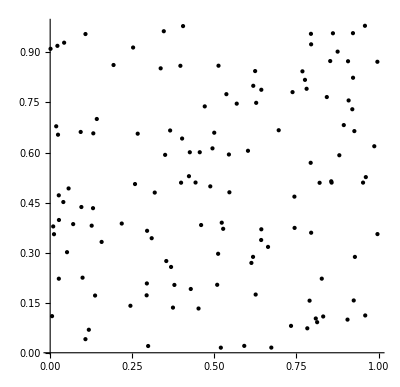

```mathematica
Graphics[{PointSize[Large],Point[Table[{RandomReal[], RandomReal[]}, 128]]},Axes->True,AxesOrigin->{0,0}]
```

```mathematica
vanDerCorput[n_,b_]:=IntegerReverse[n,b]/b^IntegerLength[n,b];
hammersley[n_,b_]:=Table[{i/n,vanDerCorput[i,b]},{i,0,n-1}];
```

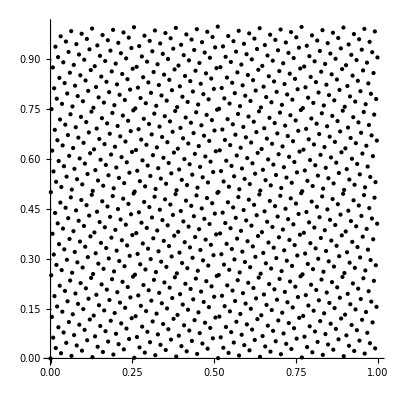

```mathematica
pts=hammersley[1000,2];
Graphics[{PointSize[Large],Point[pts]},Axes->True,AxesOrigin->{0,0}]
```

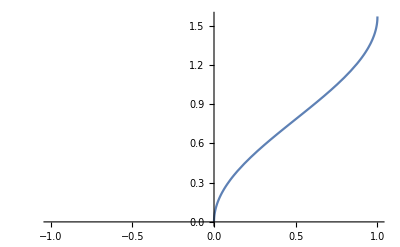

```mathematica
Plot[ArcSin[Sqrt[xi]], {xi, -1, 1}]
```

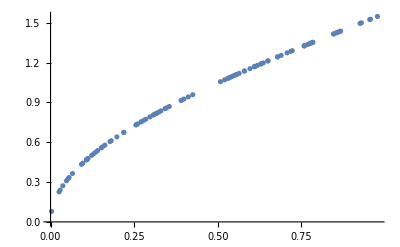

```mathematica
xitheta[]:=(
xi=RandomReal[];
theta=ArcCos[1-xi];(*ArcSin[Sqrt[xi]];*)
{xi, theta}
)
ListPlot[Table[xitheta[],100]]
```

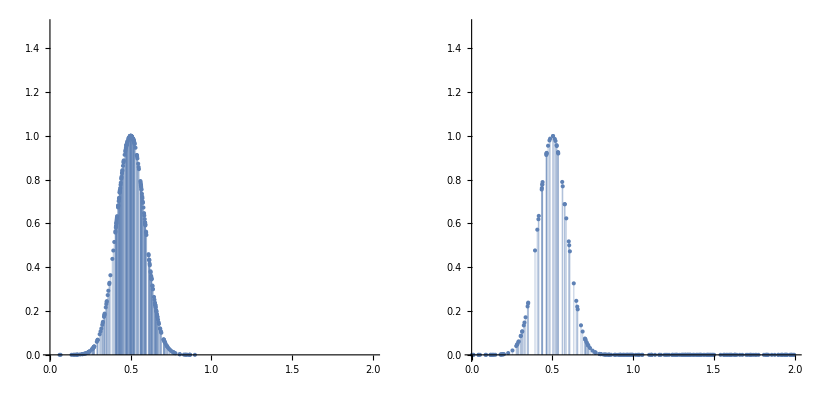

| Integral | Abs Error
Importance | 0.229095 | 0.00753786
Uniform | 0.23566 | 0.0141032

```mathematica
SeedRandom[0];
b=2;
a=0;
func[x_]:=1/Exp[(x*8-4)^2];
pdfImportance[x_]:=2.262/Exp[(x*4-2)^2];
pdfUniform[x_]:=1/(b-a);
nSamples=256;
sampleImportance[]:=(
xi=(2-InverseErf[1-2*RandomReal[]])/4(*RandomReal[]*b+a*);
{xi, func[xi]}
)
samplesImportance=Table[sampleImportance[], nSamples];
integralImportance=Total[MapThread[#1[[2]]/pdf[#1[[1]]]&,{samplesImportance}]]/nSamples;
sampleUniform[]:=(
xi=RandomReal[]*b+a;
{xi, func[xi]}
)
samplesUniform=Table[sampleUniform[], nSamples];
GraphicsGrid[{{ListPlot[samplesImportance,Filling->Axis,AspectRatio->1,PlotRange->{{a, b},{0,1.5}}],
ListPlot[samplesUniform,Filling->Axis,AspectRatio->1,PlotRange->{{a, b},{0,1.5}}]}}]
integralUniform=Total[MapThread[#1[[2]]/pdfUniform[#1[[1]]]&,{samplesUniform}]]/nSamples;
TableForm[{{integralImportance, Abs[Integrate[func[x], {x, a, b}]-integralImportance]},
{integralUniform,Abs[Integrate[func[x], {x, a, b}]-integralUniform]}},TableHeadings->{{"Importance","Uniform"},{"Integral", "Abs Error"}}]
```

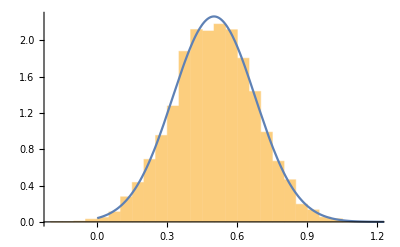

```mathematica
Show[Histogram[Table[(2-InverseErf[1-2*RandomReal[]])/4, 10000],30,"PDF"], Plot[pdf[x], {x, a, b}, PlotRange->Full]]
```

{{-1,0},{0.5,(√3)/2},{0.5,-(√3)/2}}

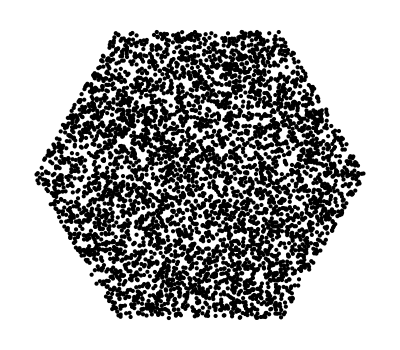

```mathematica
vectors={{-1,0},{0.5,Sqrt[3]/2},{0.5,-Sqrt[3]/2}}
randInHex[]:=
(
x=Ceiling[RandomReal[]*3];
v1=vectors[[x]];
v2= vectors[[Mod[x+1, 3]+1]];
p1=RandomReal[];
p2=RandomReal[];
{p1*v1[[1]]+p2*v2[[1]],p1*v1[[2]]+p2*v2[[2]]}
)
Graphics[{Point[Table[randInHex[],5000]]}]
```

```mathematica
vectors={{-1,0},{0.5,Sqrt[3]/2},{0.5,-Sqrt[3]/2}}//N
```

{{-1.,0.},{0.5,0.866025},{0.5,-0.866025}}

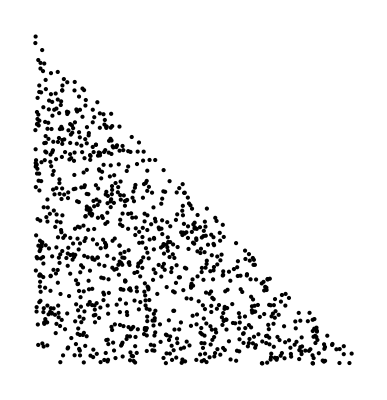

```mathematica
randInHex[]:=
(

v1={-1,1};
v2= {1, 1};
p1=Sqrt[RandomReal[]];
p2=RandomReal[];
{1-p1,p2*p1}
)
Graphics[{Point[Table[randInHex[],1000]]}]
```

```mathematica
SphericalToDecart[theta_, phi_]:={Cos[phi] Sin[theta], Sin[theta] Sin[phi], Cos[theta]}

Reflect[vec_, n_]:=vec-2*Dot[vec, n]*n;
ggx[wi_,theta_,phi_, alpha_]:=(
dir=SphericalToDecart[theta, phi];
wo=Reflect[-wi, {0, 0, 1}];
cosTheta=Dot[wo, dir];
alpha^2/(π ((alpha^2-1) cosTheta^2+1)^2)
)
SampleGGX[wi_,alpha_]:=(
phi=2*Pi*RandomReal[];
xi=RandomReal[];
cosTheta=Sqrt[(1-xi)/(xi*(alpha^2-1)+1)];
sinTheta=Sqrt[Max[0,1-cosTheta*cosTheta]];
result=Reflect[-wi,{Cos[phi]*sinTheta,Sin[phi]*sinTheta,cosTheta}];
resSpherical=ToSphericalCoordinates[result];
r=ggx[wi,resSpherical[[2]],resSpherical[[3]], alpha];
{{0, 0, 0},result*r}
)
```

```mathematica
wi=Normalize[{0.5, -0.5, 0.25}];
alpha=0.3;
Show[
Graphics3D[{
RGBColor[{0.9, 0.9, 0.9}], Polygon[{-s-t,-s+t,s+t,s-t}],
Table[{Black,Arrowheads[0.02],Arrow[SampleGGX[wi,alpha]]}, 100],
Thick, Blue,Arrow[{{0,0,0},n}],Black,Text[Style["n",40, FontFamily->"Cambria Math"],n*1.2],
Thick, Red,Arrow[{{0,0,0},s}],Black,Text[Style["s",40, FontFamily->"Cambria Math"],s*1.2],
Thick, Green,Arrow[{{0,0,0},t}],Black,Text[Style["t",40, FontFamily->"Cambria Math"],t*1.2],
Thick, Purple,Arrow[{wi,{0,0,0}}], ,Black,Text[Style["ω_i",40, FontFamily->"Cambria Math"],wi*1.2]
},Axes->False, Lighting->"Neutral", Boxed->False, ViewPoint->{2, 2, 1}, ViewCenter->{0, 0, 0}, ViewVertical->{0,0,1}], 
SphericalPlot3D[
ggx[wi,θ,ϕ,alpha]/1,
{θ,0,π/2},{ϕ,0,2 π}, PlotStyle->{Opacity[0.0]},PlotPoints->50]
]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
phi=2*Pi*e1;
theta=ArcCos[Sqrt[(1-e2)/(e2*(alpha*alpha-1)+1)]];
Reflect[wi, SphericalToDecart[phi, theta]],
{e1,0,1},{e2,0,1},PlotRange->All]
```

-Graphics3D-

```mathematica
Reflect[vec_, n_]:=vec-2*Dot[vec, n]*n;
wo=Normalize[{-1, 1, 1}];
wi=Reflect[-wo, n];
Show[
Graphics3D[{
(*Table[{Black,Arrow[SampleHemisphereOriented[n]]}, 10],*)
RGBColor[{0.9, 0.9, 0.9}], Polygon[{-s-t,-s+t,s+t,s-t}],
Thick, Blue,Arrow[{{0,0,0},n}],Black,Text[Style["n",40, FontFamily->"Cambria Math"],n*1.2],
Thick, Red,Arrow[{{0,0,0},s}],Black,Text[Style["s",40, FontFamily->"Cambria Math"],s*1.2],
Thick, Green,Arrow[{{0,0,0},t}],Black,Text[Style["t",40, FontFamily->"Cambria Math"],t*1.2],
Thick, Purple,Arrow[{wi,{0,0,0}}],Black,Text[Style["ω_i",40, FontFamily->"Cambria Math"],wi*1.2],
Thick, Purple,Arrow[{{0,0,0}, wo}],Black,Text[Style["ω_o",40, FontFamily->"Cambria Math"],wo*1.2],
Black,Text[Style["p",40, FontFamily->"Cambria Math"],{0, 0,-0.1}],
Arc3D[0.3,{{0,0,1},wi,{0, 0, 0}},20],
Arc3D[0.275,{{0,0,1},wi,{0, 0, 0}},20],
Arc3D[0.3,{wo,{0,0,1},{0, 0, 0}},20]
},Axes->False, Lighting->"Neutral", Boxed->False, ViewPoint->{2, 2, 1}, ViewCenter->{0, 0, 0}, ViewVertical->{0,0,1}]
]
```

-Graphics3D-

```mathematica
{a,b,m}={{1,0,0},{-1,1,2},{1,1,1}};
Arc3D[nn_,{a_,b_,m_},n_: 60,prim_: Line]:=Module[{α,lab,axis,aarc,tm,alpha},lab=m+Norm[a-m]*Normalize[b-m];
axis=(a-m)×(b-m);
aarc=(VectorAngle[a-m,b-m]);
tm=RotationMatrix[alpha,axis]*nn;
prim@Table[m+tm.(a-m),{alpha,0,aarc,aarc/n}]]

Graphics3D[{PointSize[Large],Line[{m,a}],Line[{m,b}],Point[{a,b,m}],Arc3D[2,{a,b,m},20]}]
```

-Graphics3D-

```mathematica
Show[
Graphics3D[{
RGBColor[{0.9, 0.9, 0.9}], Polygon[{-s-t,-s+t,s+t,s-t}],
Thick, Blue,Arrow[{{0,0,0},n}],Black,Text[Style["n",40, FontFamily->"Cambria Math"],n*1.2],
Thick, Red,Arrow[{{0,0,0},s}],Black,Text[Style["s",40, FontFamily->"Cambria Math"],s*1.2],
Thick, Green,Arrow[{{0,0,0},t}],Black,Text[Style["t",40, FontFamily->"Cambria Math"],t*1.2],
Thick, Purple,Arrow[{wi,{0,0,0}}], ,Black,Text[Style["ω_i",40, FontFamily->"Cambria Math"],wi*1.2]
},Axes->False, Lighting->"Neutral", Boxed->False, ViewPoint->{2, 2, 1}, ViewCenter->{0, 0, 0}, ViewVertical->{0,0,1}], 
SphericalPlot3D[
ggx[wi,θ,ϕ,alpha]/1,
{θ,0,π/2},{ϕ,0,2 π}, PlotStyle->{Purple,Opacity[0.3]},PlotPoints->50]
]
```

-Graphics3D-

```mathematica
Show[
Graphics3D[{
RGBColor[{0.9, 0.9, 0.9}], Polygon[{-s-t,-s+t,s+t,s-t}],
Thick, Blue,Arrow[{{0,0,0},n}],Black,Text[Style["n",40, FontFamily->"Cambria Math"],n*1.2],
Thick, Red,Arrow[{{0,0,0},s}],Black,Text[Style["s",40, FontFamily->"Cambria Math"],s*1.2],
Thick, Green,Arrow[{{0,0,0},t}],Black,Text[Style["t",40, FontFamily->"Cambria Math"],t*1.2],
Thick, Purple,Arrow[{wi,{0,0,0}}], ,Black,Text[Style["ω_i",40, FontFamily->"Cambria Math"],wi*1.2]
},Axes->False, Lighting->"Neutral", Boxed->False, ViewPoint->{2, 2, 1}, ViewCenter->{0, 0, 0}, ViewVertical->{0,0,1}], 
SphericalPlot3D[1,{θ,0,π/2},{ϕ,0,2 π}, PlotStyle->{Purple,Opacity[0.3]}]
]
```

-Graphics3D-